## relation between latent and infectious period and generation time for compartmental models

### For an SI^kR model, the time from becoming infectious to infection in a compartmental model with k stages of infection and a per stage rate q follows a distribution which has the following Laplace transform (see e.g. Svensson Math Biosci 2008)

```mathematica
lapl[t_]:=(1-(1+q t)^(-k))/(q k t)
```

```mathematica
InverseLaplaceTransform[lapl[t],t,x]
```

Gamma[k,x/q]/(k q Gamma[k])

example  of  the  shape  of  this  distribution

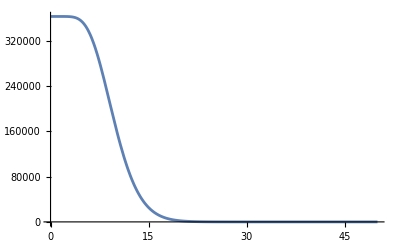

```mathematica
Plot[Gamma[10,x],{x,0,50}]
```

The  moment  generating  function  is  the  Laplace  transform  with  the  sign  of  the  argument  reversed

```mathematica
momgenfun[s_]:=lapl[-s]
```

```mathematica
momgenfun[s]
```

-(1-(1-q s)^-k)/(k q s)

The  cumulant generating function is the logarithm of the moment  generating  function

```mathematica
cumgenfun[s_]=Log[Simplify[lapl[-s]]]
```

Log[-(1-(1-q s)^-k)/(k q s)]

```mathematica
cumgenfun2[s_]:=Log[((1-q s)^-k-1)/(k q s)]
```

The  mean and variance of the distribution are given by the first and second derivative of the cumulant generating function evaluated at zero

mean (confirming results of Svensson 2008)

```mathematica
firstder[s_]:=FullSimplify[D[cumgenfun2[s],{s,1}]]
```

```mathematica
Limit[firstder[s],s->0]
```

1/2 (1+k) q

variance

```mathematica
secondder[s_]:=FullSimplify[D[cumgenfun2[s],{s,2}]]
```

```mathematica
Limit[secondder[s],s->0]
```

1/12 (5+6 k+k^2) q^2

### For an SE^k1I^k2R model, the time from becoming infectious to infection in a compartmental model with k1 latent stages, k2 stages of infection, and a per stage rate q follows a distribution which has the following Laplace transform

```mathematica
laplgentime[t_]:=((1+q t)^(-k1))(1-(1+q t)^(-k2))/(q k2 t)
```

```mathematica
InverseLaplaceTransform[laplgentime[t],t,x]
```

(-Gamma[k1,x/q]/Gamma[k1]+Gamma[k1+k2,x/q]/Gamma[k1+k2])/(k2 q)

example  of  the  shape  of  this  distribution

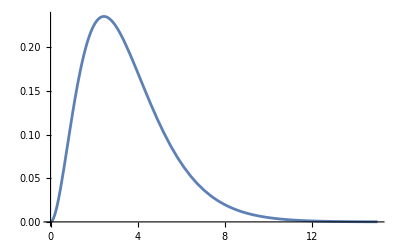

```mathematica
Plot[(Gamma[4,x]/Gamma[4]-Gamma[2,x]/Gamma[2])/2,{x,0,15}]
```

The  moment  generating  function  is  the  Laplace  transform  with  the  sign  of  the  argument  reversed

```mathematica
momgenfungentime[s_]:=laplgentime[-s]
```

```mathematica
momgenfungentime[s]
```

-((1-q s)^-k1 (1-(1-q s)^-k2))/(k2 q s)

The  cumulant generating function is the logarithm of the moment  generating  function

```mathematica
cumgenfungentime[s_]=Log[Simplify[laplgentime[-s]]]
```

Log[-((1-q s)^(-k1-k2) (-1+(1-q s)^k2))/(k2 q s)]

```mathematica
Limit[cumgenfungentime[s],s->0]
```

0

The  mean and variance of the distribution are given by the first and second derivative of the cumulant generating function evaluated at zero

mean

```mathematica
firstdergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,1}]]
```

```mathematica
Limit[firstdergentime[s],s->0]
```

1/2 (1+2 k1+k2) q

example

```mathematica
1/2 (1+2 k1+k2) q /.{k1->2,k2->2,q->1}
```

7/2

variance

```mathematica
seconddergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,2}]]
```

```mathematica
Limit[seconddergentime[s],s->0]
```

1/12 (5+12 k1+6 k2+k2^2) q^2

example

```mathematica
1/12 (5+12 k1+6 k2+k2^2) q /.{k1->2,k2->2,q->1}
```

### For an SE^k1I^k2R model, the time from becoming infectious to infection in a compartmental model with k1 latent stages and a latent stage rate q1, k2 stages of infection and an infectious per stage rate q2 follows a distribution which has the following Laplace transform

```mathematica
laplgentime[t_]:=((1+q1 t)^(-k1))(1-(1+q2 t)^(-k2))/(q2 k2 t)
```

```mathematica
InverseLaplaceTransform[laplgentime[t],t,x]
```

(1-Gamma[k1,x/q1]/Gamma[k1]-InverseLaplaceTransform[((1+q1 t)^-k1 (1+q2 t)^-k2)/t,t,x])/(k2 q2)

The  moment  generating  function  is  the  Laplace  transform  with  the  sign  of  the  argument  reversed

```mathematica
momgenfungentime[s_]:=laplgentime[-s]
```

```mathematica
momgenfungentime[s]
```

-((1-q1 s)^-k1 (1-(1-q2 s)^-k2))/(k2 q2 s)

The  cumulant generating function is the logarithm of the moment  generating  function

```mathematica
cumgenfungentime[s_]=Log[Simplify[laplgentime[-s]]]
```

Log[-((1-q1 s)^-k1 (1-(1-q2 s)^-k2))/(k2 q2 s)]

```mathematica
Limit[cumgenfungentime[s],s->0]
```

0

The  mean and variance of the distribution are given by the first and second derivative of the cumulant generating function evaluated at zero

mean

```mathematica
firstdergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,1}]]
```

```mathematica
Limit[firstdergentime[s],s->0]
```

1/2 (2 k1 q1+q2+k2 q2)

variance

```mathematica
seconddergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,2}]]
```

```mathematica
Limit[seconddergentime[s],s->0]
```

k1 q1^2+1/12 (5+6 k2+k2^2) q2^2

higher  derivatives  are  not  very  informative

```mathematica
thirddergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,3}]]
```

```mathematica
Limit[seconddergentime[s],s->0]
```

k1 q1^2+1/12 (5+6 k2+k2^2) q2^2

```mathematica
fourthdergentime[s_]:=FullSimplify[D[cumgenfungentime[s],{s,4}]]
```

```mathematica
Limit[seconddergentime[s],s->0]
```

k1 q1^2+1/12 (5+6 k2+k2^2) q2^2